```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v3/phase/phase_boundaryv2

```mathematica
mf=Table[Transpose[Import["./TemB"<>ToString[i]<>"/BUFFER/MF.DAT"]][[1]],{i,1,36}];
intdmfdt=Table[-D[Interpolation[mf[[i]]][x],x],{i,1,36}];
mub=Flatten[Table[i*15,{i,1,36}]];
Tpc=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[2]][[1]][[2]],{i,1,36}];
peak=Table[FindMaximum[{intdmfdt[[i]],90<x<170},{x,140}][[1]],{i,1,36}];
Tpcup80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]+2}][[1]][[2]],{i,1,36}];
Tpcdown80=Table[FindRoot[intdmfdt[[i]]==peak[[i]]*0.8,{x,Tpc[[i]]-5}][[1]][[2]],{i,1,36}];
fitTpc=FindFit[Transpose[{mub,Tpc}],a+b x^2+c x^4(*+d x^6*),{a,b,c},x];
fitTpcup=FindFit[Transpose[{mub,Tpcup80}],a+b x^2+c x^4,{a,b,c},x];
fitTpcdown=FindFit[Transpose[{mub,Tpcdown80}],a+b x^2+c x^4,{a,b,c},x];
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

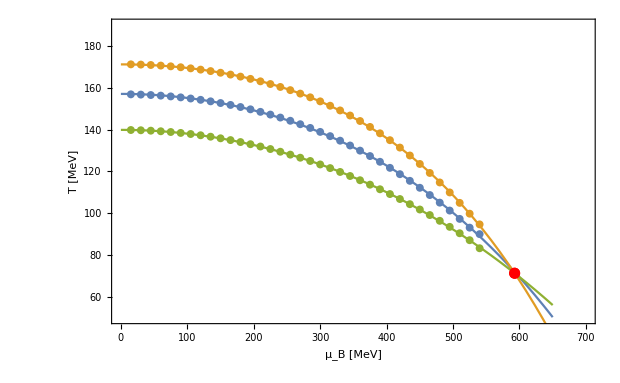

./parav2.pdf

```mathematica
Show[ListPlot[{Transpose[{mub,Tpc}],Transpose[{mub,Tpcup80}],Transpose[{mub,Tpcdown80}]},PlotRange->{{0,700},{50,190}}],Plot[{a+b x^2+c x^4/.fitTpc,a+b x^2+c x^4/.fitTpcup,a+b x^2+c x^4/.fitTpcdown},{x,0,650}],ListPlot[{{592.7,71.3}},PlotStyle->Red],Frame->True,FrameLabel->{Style["μ_B [MeV]",15,Black],Style["T [MeV]",15,Black]}]
Export["./parav2.pdf",%]
```

```mathematica
FindRoot[(a+b x^2+c x^4/.fitTpcup)==(a+b x^2+c x^4/.fitTpcdown),{x,600}]
```

{x→592.742}

```mathematica
a+b x^2+c x^4/.fitTpcup/.{x->592.7424837645036}
```

71.3182